# Ratio of relative velocity v to the speed of light c in 1D

-Graphics-

## In 1D

### Speed of light

```mathematica
c=299792458;
```

### Relative velocity between inertial reference frames

```mathematica
v=0.9c;
```

### Ratio of relative velocity v to the speed of light c

```mathematica
β[𝓋_]=𝓋/c;
```

```mathematica
β[v]
```

0.9

```mathematica
βPlot1=Plot[β[v],{v,0,c},FrameLabel->{"v (m/s)","β"},PlotLegends->"Expressions",Frame-> True,GridLines->Automatic,AspectRatio->1];
```

```mathematica
βPlot2=ListPlot[{{v,β[v]}},MeshStyle->Red,PlotMarkers->{Automatic,Medium},Frame-> True,GridLines->Automatic,AspectRatio->1];
```

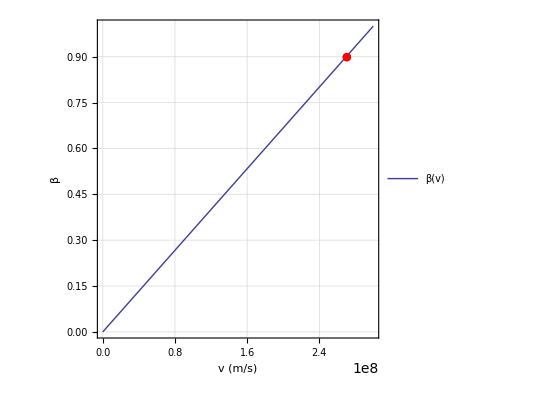

```mathematica
Show[βPlot1,βPlot2]
```

```mathematica
Limit[β[𝓋],𝓋->c]
```

1